```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210407_sliding_time_windows_and_OR_model"];
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
boundaries=ConstantArray[{0,500},fluxexchanges];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=RandomInteger[{1,fluxexchanges}];
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}]]
```

```mathematica
AbsoluteTiming[sequences=Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,300],200];]
```

{2278.94,Null}

```mathematica
sequenceschopped=Chop[sequences,10^-5];
```

```mathematica
datafull=Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Flatten[sequenceschopped,1][[All,Range@1008]],2];
```

```mathematica
(* datafull=Import["OR_model_dataset_2.mx"]; *)
```

```mathematica
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
testrows=datafull[[first@datafull,All]];
testcolumns=datafull[[All,first[datafullᵀ]]];
```

```mathematica
Dimensions@datafull
Dimensions@testrows
Dimensions@testcolumns
```

{60000,1010}

{60000,1010}

{60000,5}

```mathematica
rowduplicates=DeleteDuplicates@Cases[testcolumns[[All,{3,4,5}]],{x_,y_,z_}/;x==y&&y==z]
```

{{0,0,0}}

```mathematica
datachopped=Delete[testcolumns,Position[testcolumns[[All,{3,4,5}]],Flatten[rowduplicates,1]]];
datachopped=datachopped[[All,{1,2,4,5}]];
Dimensions@datachopped
```

{39136,4}

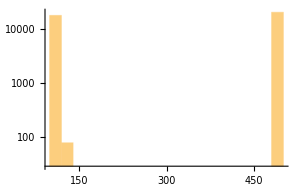
{-Graphics-,-Graphics-}

```mathematica
Table[Histogram[datachopped[[All,i]],ScalingFunctions->"Log",PlotRange->All,ImageSize->300],{i,{3,4}}]
```

```mathematica
datachoppedfinal=Delete[datachopped,Position[datachopped[[All,{3,4}]],{x_,y_}/;x>200||y>200]];
```

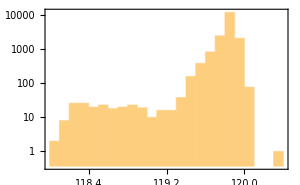
{-Graphics-,-Graphics-}

```mathematica
Table[Histogram[datachoppedfinal[[All,i]],ScalingFunctions->"Log",Frame->True,PlotRange->All,ImageSize->300],{i,{3,4}}]
```

```mathematica
datafull=datachoppedfinal;
Dimensions@datafull
```

{18300,4}

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
x2=Round@Ceiling[Length@datafull/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,3,0.02,win2];]
```

{3.07675,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,2,50,Green],{i,Range@win2}];
graphsandnodenumbers
```

{{-Graphics-,42},{-Graphics-,86},{-Graphics-,82},{-Graphics-,29},{-Graphics-,31},{-Graphics-,21},{-Graphics-,16},{-Graphics-,29},{-Graphics-,30},{-Graphics-,27},{-Graphics-,14},{-Graphics-,11},{-Graphics-,11},{-Graphics-,21},{-Graphics-,22},{-Graphics-,14},{-Graphics-,27},{-Graphics-,66},{-Graphics-,82},{-Graphics-,71},{-Graphics-,34},{-Graphics-,12},{-Graphics-,30},{-Graphics-,31},{-Graphics-,34},{-Graphics-,25},{-Graphics-,25},{-Graphics-,20},{-Graphics-,34},{-Graphics-,42},{-Graphics-,40},{-Graphics-,30},{-Graphics-,22},{-Graphics-,13},{-Graphics-,13},{-Graphics-,17},{-Graphics-,20}}

```mathematica
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{1216.89,Null}

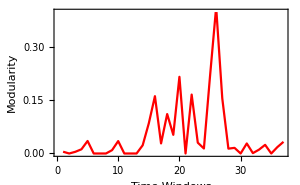
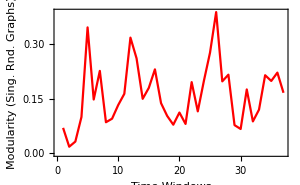
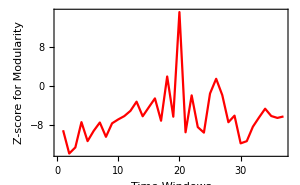

```mathematica
{ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,FrameLabel->{"Time Windows","Modularity"},PlotStyle->Red,ImageSize->300,PlotRange->{All,{0,0.4}}],
ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,PlotStyle->Red,ImageSize->300,PlotRange->All,FrameLabel->{"Time Windows","Modularity (Sing. Rnd. Graphs)"}],
ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,FrameLabel->{"Time Windows","Z-score for Modularity"},PlotStyle->Red,ImageSize->300,PlotRange->All]}
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,3,30,win2];]
```

{0.580351,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],2,2,50,Green],{i,Range@win2}];
graphsandnodenumbers
```

{{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30}}

```mathematica
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{2447.26,Null}

```mathematica
singlerandomcommmodularityvalues2=ReplacePart[singlerandomcommmodularityvalues2,{{5},{16}}->0];
Zscoresmodularity2=ReplacePart[Zscoresmodularity2,{{5},{16}}->0];
```

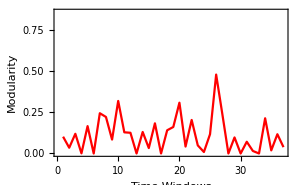
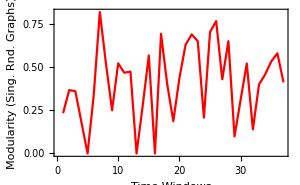
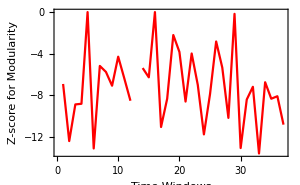

```mathematica
{ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,FrameLabel->{"Time Windows","Modularity"},PlotStyle->Red,ImageSize->300,PlotRange->{All,{0,0.86}}],
ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,PlotStyle->Red,ImageSize->300,PlotRange->All,FrameLabel->{"Time Windows","Modularity (Sing. Rnd. Graphs)"}],
ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,FrameLabel->{"Time Windows","Z-score for Modularity"},PlotStyle->Red,ImageSize->300,PlotRange->All]}
```